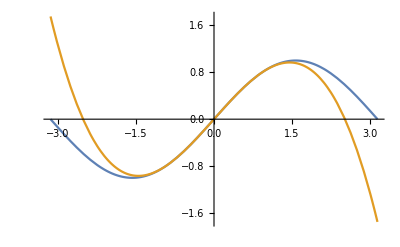

```mathematica
e[l_,x_]:=Sqrt[(2*l+1)/2]*LegendreP[l,x];
sin[x_]:=Sum[NIntegrate[Sin[y]*e[l,y],{y,-1,1}]*e[l,x],{l,0,3}];
Plot[{Sin[x],sin[x]},{x,-Pi,Pi}]
```